# -Graphics-

# Wolfram 语言编程：概念到应用

## 基本概念和函数

-Graphics-

## 学习目标

### 表达式

原子元素

一切都是表达式

使用表达式： Head、Length 和 Part

表达式和用法的级别

### 赋值

直接与延迟赋值

清除值

### 一些基本函数

迭代

计数和分组

### 列表与关联

构建和操作列表

构建一个 Association

Association 中的各种操作

创建关联的函数

Dataset

# 表达式

## 原子元素

Wolfram 语言™ 中的所有表达式最终都是由少量不同类型的原子元素构建.

Integer

Real

String

Rational

Symbol

AtomQ 可用于检测一个表达式是否是一个原子：

```mathematica
10  (* 整数 *)
AtomQ[%]
Head[%%]
```

10

True

Integer

```mathematica
12.5 (* 实数 *)
AtomQ[%]
Head[%%]
```

12.5

True

Real

```mathematica
"Wish you a wonderful day" (* 字符串 *)
AtomQ[%]
Head[%%]
```

Wish you a wonderful day

True

String

```mathematica
1/2 (* 有理数 *)
AtomQ[%]
Head[%%]
```

1/2

True

Rational

### 符号

符号是符号型数据的最终原子：

```mathematica
var
AtomQ[%]
Head[%%]
```

var

True

Symbol

符号可以被运算：

```mathematica
a^2+a^2+a^2
```

3 a^2

可以赋值：

```mathematica
var=10;
```

```mathematica
var
```

10

```mathematica
var+10
```

20

例子：

```mathematica
{Plot, x2, String, $Version, αβγ}
```

```mathematica
x2=10
```

10

```mathematica
2x
```

当符号名称被识别时，语法颜色从蓝色变成黑色.

符号的名称：

由字母、数字和其他字符组成 .

不能以数字开头.

不能包含某些保留的特殊字符（例如：!, @, #, %, ^, +, -, _, =, &, (, ), {, }, [, ], 等）.

```mathematica
ClearAll["Global`*"]
```

## 表达式

可以使用原子对象构建更多的表达式.

#### 数学公式

```mathematica
x^2+y^2
```

```mathematica
AtomQ[x^2+y^2]
```

False

检查完全格式：

```mathematica
FullForm[x^2+y^2]
```

Plus[Power[x,2],Power[y,2]]

上面表达式的原子对象：

整数： 2
符号： Plus、Power、x 和 y

#### 代码

```mathematica
Clear[x,y]
If[x>y,"x is greater","y is greater"];
AtomQ[%]
```

False

原子对象：

```mathematica
FullForm[If[x>y,"x is greater","y is greater"]]
```

If[Greater[x,y],"x is greater","y is greater"]

原子对象：

字符串： "x is greater", "y is greater"
符号： If、Greater、x 和 y

#### 数据结构：List

```mathematica
{1,2,10.8,50};
AtomQ[%]
```

False

```mathematica
FullForm[{1,2,10.8,50}]
```

List[1,2,10.8,50]

原子对象：

整数： 1, 2, 50
实数： 10.8
符号： List

```mathematica
ClearAll["Global`*"]
```

## 一切都是表达式

Wolfram 语言中的每个对象都有相同的基本结构，称之为表达式
(一切都是表达式).
			
			f[e1, e2, e3,...]

e1、e2、e3 可以是原子对象或表达式自身.

e1: ef1[e1s1, e1s2, e1s3...]
e2: ef2[e2s1, e2s2, e2s3...]
e3: ef3[e3s1, e3s2, e3s3...]

常规形式如下：

-Graphics-

其中 F_i 和 x_i 是原子对象.

### 范例

```mathematica
a+b^c//FullForm
```

Plus[a,Power[b,c]]

```mathematica
If[5>1,"true","false"]//FullForm//HoldForm
```

If[Greater[5,1],"true","false"]

```mathematica
{1,1,2,3,5,8,13}//FullForm
```

List[1,1,2,3,5,8,13]

```mathematica
10^4+4 10^3 20+6 10^2 20^2//FullForm//HoldForm
```

Plus[Power[10,4],Times[4,Power[10,3],20],Times[6,Power[10,2],Power[20,2]]]

```mathematica
(x=2)//FullForm//HoldForm
```

Set[x,2]

```mathematica
(x=2;
y=3;
z=(x+y)^2)//FullForm//HoldForm
```

CompoundExpression[Set[x,2],Set[y,3],Set[z,Power[Plus[x,y],2]]]

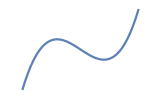
```mathematica
-Graphics-//FullForm
```

Graphics[List[List[List[],List[],Annotation[List[RGBColor[0.368417,0.506779,0.709798],AbsoluteThickness[1.6],Opacity[1.],Line[List[List[-2.64916,-79.9704],List[-2.63533,-77.8516],List[-2.51845,-61.7569],List[-2.39167,-46.2406],List[-2.27335,-33.4958],List[-2.14512,-21.4783],List[-2.01922,-11.3962],List[-2.01739,-11.2613],List[-2.01555,-11.1268],List[-2.01188,-10.8588],List[-2.00454,-10.3267],List[-1.98987,-9.27884],List[-1.96051,-7.24721],List[-1.90179,-3.43615],List[-1.8998,-3.31281],List[-1.89781,-3.18984],List[-1.89383,-2.94504],List[-1.88588,-2.45992],List[-1.86996,-1.50757],List[-1.83812,0.326257],List[-1.77446,3.71611],List[-1.7726,3.80954],List[-1.77074,3.90267],List[-1.76703,4.088],List[-1.7596,4.45502],List[-1.74474,5.17451],List[-1.71502,6.55586],List[-1.71316,6.63966],List[-1.7113,6.72317],List[-1.70759,6.88931],List[-1.70016,7.21805],List[-1.6853,7.86147],List[-1.65558,9.09266],List[-1.65376,9.1657],List[-1.65194,9.23848],List[-1.6483,9.3832],List[-1.64101,9.66936],List[-1.62645,10.2287],List[-1.59731,11.2956],List[-1.59549,11.36],List[-1.59367,11.4242],List[-1.59003,11.5517],List[-1.58274,11.8036],List[-1.56818,12.2948],List[-1.53904,13.2274],List[-1.53707,13.2883],List[-1.53509,13.3488],List[-1.53114,13.4691],List[-1.52324,13.706],List[-1.50743,14.1655],List[-1.47582,15.0282],List[-1.47384,15.0797],List[-1.47187,15.1308],List[-1.46792,15.2323],List[-1.46002,15.4318],List[-1.44421,15.8172],List[-1.4126,16.5341],List[-1.41076,16.5737],List[-1.40891,16.613],List[-1.40522,16.6911],List[-1.39785,16.8443],List[-1.3831,17.1393],List[-1.35361,17.6843],List[-1.35176,17.7164],List[-1.34992,17.7482],List[-1.34623,17.8113],List[-1.33886,17.9346],List[-1.32411,18.1704],List[-1.29462,18.599],List[-1.29262,18.626],List[-1.29062,18.6527],List[-1.28662,18.7054],List[-1.27863,18.8076],List[-1.26264,19.],List[-1.26065,19.0229],List[-1.25865,19.0455],List[-1.25465,19.0901],List[-1.24666,19.1761],List[-1.23067,19.3364],List[-1.22867,19.3553],List[-1.22667,19.374],List[-1.22268,19.4106],List[-1.21469,19.4809],List[-1.21269,19.4979],List[-1.21069,19.5146],List[-1.20669,19.5473],List[-1.1987,19.6099],List[-1.1967,19.625],List[-1.1947,19.6398],List[-1.19071,19.6687],List[-1.18271,19.7236],List[-1.16673,19.8222],List[-1.16477,19.8333],List[-1.1628,19.8441],List[-1.15888,19.8651],List[-1.15103,19.9045],List[-1.14907,19.9137],List[-1.14711,19.9228],List[-1.14319,19.9403],List[-1.13534,19.9726],List[-1.13338,19.9801],List[-1.13142,19.9874],List[-1.12749,20.0013],List[-1.12553,20.008],List[-1.12357,20.0144],List[-1.11965,20.0267],List[-1.11768,20.0325],List[-1.11572,20.038],List[-1.1118,20.0485],List[-1.10984,20.0535],List[-1.10788,20.0582],List[-1.10395,20.067],List[-1.10199,20.0711],List[-1.10003,20.0749],List[-1.09807,20.0786],List[-1.0961,20.082],List[-1.09414,20.0853],List[-1.09218,20.0883],List[-1.08826,20.0937],List[-1.0863,20.0961],List[-1.08433,20.0983],List[-1.08237,20.1003],List[-1.08041,20.1021],List[-1.07845,20.1036],List[-1.07649,20.105],List[-1.07453,20.1061],List[-1.07256,20.1071],List[-1.0706,20.1078],List[-1.06864,20.1083],List[-1.06668,20.1086],List[-1.06472,20.1088],List[-1.06276,20.1087],List[-1.06079,20.1084],List[-1.05883,20.1079],List[-1.05687,20.1072],List[-1.05491,20.1063],List[-1.05295,20.1052],List[-1.05099,20.1039],List[-1.04902,20.1023],List[-1.04706,20.1006],List[-1.0451,20.0987],List[-1.04314,20.0966],List[-1.04118,20.0943],List[-1.03935,20.0919],List[-1.03752,20.0894],List[-1.03386,20.0839],List[-1.03203,20.0808],List[-1.0302,20.0776],List[-1.02654,20.0707],List[-1.02471,20.067],List[-1.02288,20.0631],List[-1.01922,20.0548],List[-1.0119,20.0361],List[-1.01007,20.031],List[-1.00824,20.0258],List[-1.00459,20.0148],List[-0.997268,19.9907],List[-0.995438,19.9843],List[-0.993609,19.9777],List[-0.98995,19.964],List[-0.982632,19.9346],List[-0.980802,19.9269],List[-0.978973,19.9189],List[-0.975314,19.9026],List[-0.967995,19.868],List[-0.966166,19.8589],List[-0.964336,19.8497],List[-0.960677,19.8308],List[-0.953359,19.791],List[-0.95153,19.7806],List[-0.9497,19.7701],List[-0.946041,19.7487],List[-0.938723,19.7038],List[-0.924087,19.6065],List[-0.922103,19.5926],List[-0.920118,19.5784],List[-0.91615,19.5496],List[-0.908212,19.4899],List[-0.892338,19.3617],List[-0.890354,19.3449],List[-0.888369,19.328],List[-0.884401,19.2935],List[-0.876464,19.2224],List[-0.860589,19.072],List[-0.858605,19.0524],List[-0.85662,19.0327],List[-0.852652,18.9927],List[-0.844715,18.9107],List[-0.82884,18.7389],List[-0.797091,18.364],List[-0.795239,18.3408],List[-0.793387,18.3176],List[-0.789683,18.2706],List[-0.782274,18.1751],List[-0.767457,17.9777],List[-0.737824,17.5578],List[-0.735972,17.5305],List[-0.73412,17.5031],List[-0.730415,17.4478],List[-0.723007,17.3357],List[-0.70819,17.1055],List[-0.678556,16.6222],List[-0.676549,16.5883],List[-0.674543,16.5544],List[-0.670529,16.486],List[-0.662501,16.3477],List[-0.646446,16.0648],List[-0.614336,15.4741],List[-0.550115,14.1993],List[-0.424013,11.3784],List[-0.306371,8.44088],List[-0.178823,5.01901],List[-0.0597365,1.69076],List[0.0570117,-1.61379],List[0.183666,-5.15225],List[0.30186,-8.32349],List[0.42996,-11.5198],List[0.555721,-14.3153],List[0.557554,-14.353],List[0.559387,-14.3906],List[0.563052,-14.4656],List[0.570384,-14.6145],List[0.585046,-14.9076],List[0.614371,-15.4747],List[0.616204,-15.5093],List[0.618037,-15.5438],List[0.621703,-15.6124],List[0.629034,-15.7485],List[0.643696,-16.0155],List[0.673021,-16.5285],List[0.675009,-16.5623],List[0.676997,-16.5959],List[0.680972,-16.6627],List[0.688922,-16.7947],List[0.704823,-17.0522],List[0.736625,-17.5402],List[0.738612,-17.5694],List[0.7406,-17.5986],List[0.744575,-17.6564],List[0.752526,-17.7703],List[0.768426,-17.9909],List[0.800228,-18.4028],List[0.802084,-18.4256],List[0.803939,-18.4483],List[0.80765,-18.4932],List[0.815071,-18.5813],List[0.829915,-18.7508],List[0.83177,-18.7714],List[0.833625,-18.7918],List[0.837336,-18.8322],List[0.844758,-18.9112],List[0.859601,-19.0623],List[0.861456,-19.0805],List[0.863312,-19.0986],List[0.867023,-19.1343],List[0.874444,-19.2039],List[0.889287,-19.3358],List[0.891143,-19.3516],List[0.892998,-19.3673],List[0.896709,-19.3982],List[0.904131,-19.458],List[0.918974,-19.5702],List[0.920793,-19.5833],List[0.922612,-19.5962],List[0.926249,-19.6215],List[0.933525,-19.6704],List[0.935344,-19.6822],List[0.937162,-19.6939],List[0.9408,-19.7168],List[0.948076,-19.7607],List[0.949894,-19.7713],List[0.951713,-19.7817],List[0.955351,-19.8021],List[0.962626,-19.8409],List[0.977177,-19.911],List[0.978996,-19.919],List[0.980815,-19.9269],List[0.984453,-19.9422],List[0.991728,-19.9707],List[0.993547,-19.9775],List[0.995366,-19.984],List[0.999004,-19.9967],List[1.00628,-20.0199],List[1.0081,-20.0253],List[1.00992,-20.0306],List[1.01355,-20.0406],List[1.01537,-20.0453],List[1.01719,-20.0499],List[1.02083,-20.0585],List[1.02265,-20.0626],List[1.02447,-20.0665],List[1.02811,-20.0738],List[1.02992,-20.0771],List[1.03174,-20.0804],List[1.03538,-20.0863],List[1.03735,-20.0892],List[1.03933,-20.0919],List[1.0413,-20.0944],List[1.04328,-20.0968],List[1.04525,-20.0989],List[1.04722,-20.1008],List[1.0492,-20.1025],List[1.05117,-20.104],List[1.05314,-20.1053],List[1.05512,-20.1064],List[1.05709,-20.1073],List[1.05906,-20.1079],List[1.06104,-20.1084],List[1.06301,-20.1087],List[1.06499,-20.1088],List[1.06696,-20.1086],List[1.06893,-20.1083],List[1.07091,-20.1077],List[1.07288,-20.1069],List[1.07485,-20.1059],List[1.07683,-20.1048],List[1.0788,-20.1034],List[1.08077,-20.1017],List[1.08275,-20.0999],List[1.08472,-20.0979],List[1.0867,-20.0957],List[1.08867,-20.0932],List[1.09064,-20.0905],List[1.09262,-20.0877],List[1.09459,-20.0846],List[1.09854,-20.0777],List[1.10051,-20.074],List[1.10248,-20.0701],List[1.10643,-20.0615],List[1.10841,-20.0569],List[1.11038,-20.0521],List[1.11433,-20.0419],List[1.1163,-20.0364],List[1.11827,-20.0307],List[1.12222,-20.0187],List[1.13012,-19.9921],List[1.13209,-19.9849],List[1.13406,-19.9775],List[1.13801,-19.962],List[1.14591,-19.9283],List[1.14788,-19.9193],List[1.14985,-19.9101],List[1.1538,-19.891],List[1.16169,-19.8501],List[1.16354,-19.8401],List[1.16538,-19.8298],List[1.16906,-19.8087],List[1.17643,-19.7642],List[1.17827,-19.7525],List[1.18011,-19.7407],List[1.18379,-19.7164],List[1.19116,-19.6655],List[1.193,-19.6522],List[1.19484,-19.6388],List[1.19852,-19.6113],List[1.20589,-19.5538],List[1.22062,-19.4291],List[1.22246,-19.4126],List[1.2243,-19.3958],List[1.22799,-19.3618],List[1.23535,-19.2911],List[1.25008,-19.1397],List[1.27955,-18.7961],List[1.28154,-18.7708],List[1.28354,-18.7453],List[1.28753,-18.6935],List[1.29552,-18.5867],List[1.31149,-18.3608],List[1.31348,-18.3314],List[1.31548,-18.3018],List[1.31947,-18.2416],List[1.32746,-18.1182],List[1.34343,-17.8587],List[1.34542,-17.825],List[1.34742,-17.7911],List[1.35141,-17.7225],List[1.3594,-17.582],List[1.37537,-17.288],List[1.40731,-16.6472],List[1.40917,-16.6075],List[1.41103,-16.5677],List[1.41476,-16.4873],List[1.42222,-16.3235],List[1.43713,-15.984],List[1.46695,-15.2569],List[1.46882,-15.2093],List[1.47068,-15.1614],List[1.47441,-15.065],List[1.48187,-14.8689],List[1.49678,-14.4645],List[1.5266,-13.6056],List[1.52843,-13.5508],List[1.53026,-13.4957],List[1.53391,-13.3848],List[1.54122,-13.1599],List[1.55584,-12.6977],List[1.58508,-11.7232],List[1.58691,-11.66],List[1.58874,-11.5966],List[1.59239,-11.469],List[1.5997,-11.2106],List[1.61432,-10.6809],List[1.64356,-9.56968],List[1.64554,-9.49182],List[1.64753,-9.41363],List[1.65149,-9.25628],List[1.65942,-8.93769],List[1.67528,-8.28483],List[1.70699,-6.91572],List[1.77043,-3.91834],List[1.77228,-3.82563],List[1.77413,-3.73262],List[1.77783,-3.5457],List[1.78523,-3.16819],List[1.80003,-2.39848],List[1.82963,-0.799767],List[1.88883,2.63944],List[1.89084,2.76164],List[1.89284,2.88422],List[1.89685,3.13053],List[1.90487,3.62772],List[1.92091,4.64051],List[1.95299,6.74042],List[2.01714,11.2433],List[2.14312,21.3051],List[2.26063,32.2221],List[2.38804,45.8256],List[2.507,60.2735],List[2.62362,76.1587],List[2.64862,79.9639]]]],"Charting`Private`Tag$2997#1"]],List[],List[]],Rule[AspectRatio,Power[GoldenRatio,-1]],Rule[Axes,List[False,False]],Rule[AxesLabel,List[None,None]],Rule[AxesOrigin,List[0,0]],Rule[BaseStyle,List[]],Rule[DisplayFunction,Identity],Rule[Frame,List[List[None,None],List[None,None]]],Rule[FrameLabel,List[List[None,None],List[None,None]]],Rule[FrameTicks,List[List[Automatic,Charting`ScaledFrameTicks[List[Identity,Identity]]],List[Automatic,Charting`ScaledFrameTicks[List[Identity,Identity]]]]],Rule[GridLines,List[None,None]],Rule[GridLinesStyle,Directive[GrayLevel[0.5,0.4]]],Rule[ImagePadding,All],Rule[ImageSize,List[161.628,Automatic]],Rule[Method,List[Rule["DefaultBoundaryStyle",Automatic],Rule["DefaultMeshStyle",AbsolutePointSize[6]],Rule["ScalingFunctions",None],Rule["CoordinatesToolOptions",List[Rule["DisplayFunction",Function[List[Function[Identity[Slot[1]]][Part[Slot[1],1]],Function[Identity[Slot[1]]][Part[Slot[1],2]]]]],Rule["CopiedValueFunction",Function[List[Function[Identity[Slot[1]]][Part[Slot[1],1]],Function[Identity[Slot[1]]][Part[Slot[1],2]]]]]]]]],Rule[PlotRange,List[List[-3,3],List[-79.9704,79.9639]]],Rule[PlotRangeClipping,True],Rule[PlotRangePadding,List[List[Scaled[0.02],Scaled[0.02]],List[Scaled[0.05],Scaled[0.05]]]],Rule[Ticks,List[Automatic,Automatic]]]

```mathematica
ClearAll["Global`*"]
```

## 使用表达式

考虑以下表达式：

```mathematica
data={2,4,6,7};
mathExp=a+b+c+d;
```

```mathematica
FullForm[data]
FullForm[mathExp]
```

List[2,4,6,7]

Plus[a,b,c,d]

#### 标头

表达式中的领头元素称之为 Head：

head[elem1,elem2,elem3,...]

```mathematica
Head[data]
Head[mathExp]
```

List

Plus

#### 长度

参数的数目可以用 Length 找到：

```mathematica
Length[data]
Length[mathExp]
```

4

4

#### 部分元素

可以使用 Part[] 提取部分元素：

```mathematica
Part[data,1]
Part[mathExp,3]
```

2

c

简写形式：

```mathematica
data[[1]]
mathExp[[3]]
```

2

c

第 0 个部分是标头：

```mathematica
data[[0]]
mathExp[[0]]
```

List

Plus

## 使用表达式：嵌套表达式

#### 范例一

```mathematica
expr3 ={{x,y},{ 0, 5},{Red,Green,Blue}}
```

{{x,y},{0,5},{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]}}

```mathematica
Head[expr3]
Length[expr3]
```

List

3

使用第二个参数从第二个元素中选择子元素：

```mathematica
expr3[[2]]
```

{0,5}

```mathematica
expr3[[2,1]]
```

0

```mathematica
expr3[[3]]
```

{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]}

```mathematica
expr3[[3,1]]
```

RGBColor[1, 0, 0]

```mathematica
expr3[[3,{1,3}]]
```

{RGBColor[1, 0, 0],RGBColor[0, 0, 1]}

#### 范例二

Part 使用于任何复合表达式，不只是元素列表：

```mathematica
expr4= a +b*c/d
```

a+(b c)/d

```mathematica
FullForm[expr4]
```

Plus[a,Times[b,c,Power[d,-1]]]

```mathematica
expr4[[0]]
```

Plus

```mathematica
expr4[[1]]
```

a

```mathematica
expr4[[2]]
```

(b c)/d

```mathematica
expr4[[2,3]]
```

1/d

```mathematica
expr4[[2,2]]
```

c

```mathematica
expr4[[2,1]]
```

b

```mathematica
expr4[[2,{1,3}]]
```

b/d

```mathematica
ClearAll["Global`*"]
```

## 表达式中的级别

级别为带有嵌套元素的 Wolfram 语言表达式提供了指定特定部分的通用方法：

```mathematica
data={{a, b, c}, {{1, 2}, {3, 4}}}
```

{{a,b,c},{{1,2},{3,4}}}

```mathematica
data//FullForm
```

List[List[a,b,c],List[List[1,2],List[3,4]]]

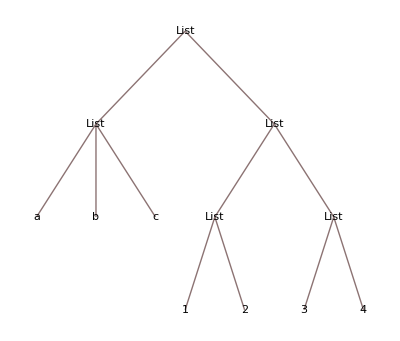

```mathematica
TreeForm[data]
```

访问单个级别：

```mathematica
Level[data,{3}]
```

{1,2,3,4}

```mathematica
Level[data,{2}]
```

{a,b,c,{1,2},{3,4}}

```mathematica
Level[data,{1}]
```

{{a,b,c},{{1,2},{3,4}}}

```mathematica
Level[data,{0}]
```

{{{a,b,c},{{1,2},{3,4}}}}

共同访问多个级别：

```mathematica
Level[data,2]
```

{a,b,c,{a,b,c},{1,2},{3,4},{{1,2},{3,4}}}

```mathematica
ClearAll["Global`*"]
```

## 使用级别的函数

### Map

语法：Map[f,expr,levelspec]

```mathematica
Map[Sqrt,{2,3,4,5,6}]
```

{√2,√3,2,√5,√6}

默认情况下，Map[] 作用于级别 1：

```mathematica
data={{a, b, c}, {{1, 2}, {3, 4}}};
TreeForm[data]
```

-Graphics-

```mathematica
Map[f, data]
```

{f[{a,b,c}],f[{{1,2},{3,4}}]}

把 Map 应用于其他级别：

```mathematica
Map[f, data,{2}] (* applied at level 2 *)
```

{{f[a],f[b],f[c]},{f[{1,2}],f[{3,4}]}}

```mathematica
Map[f, data, {3}] (* applied at level 3 *)
```

{{a,b,c},{{f[1],f[2]},{f[3],f[4]}}}

```mathematica
Map[f, data, {1}] (* applied at level 1 *)
```

{f[{a,b,c}],f[{{1,2},{3,4}}]}

```mathematica
Map[f, data, {0}] (* applied at level 0 *)
```

f[{{a,b,c},{{1,2},{3,4}}}]

```mathematica
Map[f, data, 2] (* applied at 2 and all levels above that *)
```

{f[{f[a],f[b],f[c]}],f[{f[{1,2}],f[{3,4}]}]}

```mathematica
ClearAll["Global`*"]
```

## 使用级别的函数（续）

接受 “levelspec” 参数的其他函数：

```mathematica
Module[{symbols,symbols2},
symbols=EntityValue["WolframLanguageSymbol","TextStrings","EntityAssociation"];
symbols2=CommonName@Keys@Select[symbols,AnyTrue[StringContainsQ["levelspec",IgnoreCase->True]]];
symbols3=ToString/@symbols2;
Partition[Style[#,18,"Times"]&/@symbols3,5]//Grid]
```

Apply | Cases | Catenate | Count | DeleteCases
FirstCase | FirstPosition | FreeQ | Level | Map
MapIndexed | MemberQ | ParallelMap | Position | Replace

### Cases

默认情况下，Cases[] 作用于级别 1：

```mathematica
Cases[{1,f[5.5],20,y,f[8],9,f[10]},_Integer]
```

{1,20,9}

把 Cases[] 应用于级别 2：

```mathematica
Cases[{1,1,f[a],2,3,y,f[8],9,f[10]},_Integer,{2}]
```

{8,10}

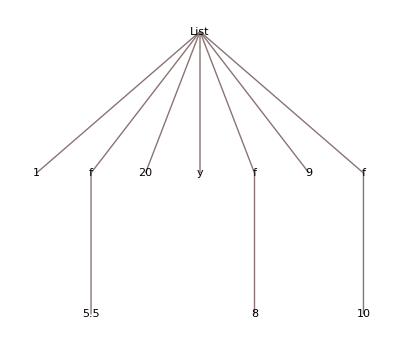

```mathematica
{1,f[5.5],20,y,f[8],9,f[10]}//TreeForm
```

### Replace

ReplaceAll[] 替代所有元素：

```mathematica
ReplaceAll[{{1,2,{3,4}},{5,6,{7,8}}},x_Integer:>x^2]
```

{{1,4,{9,16}},{25,36,{49,64}}}

Replace 需要在特定级别替代元素. 默认情况下，Replace 作用于级别 1：

把 Replace 作用于级别 2：

```mathematica
Replace[{{1,2,{3,4}},{5,6,{7,8}}},x_Integer:>x^2,{2}]
```

{{1,4,{3,4}},{25,36,{7,8}}}

把 Replace[] 作用于级别 3：

```mathematica
Replace[{{1,2,{3,4}},{5,6,{7,8}}},x_Integer:>x^2,{3}]
```

{{1,2,{9,16}},{5,6,{49,64}}}

```mathematica
ClearAll["Global`*"]
```

## Depth 和 LeafCount

#### 范例一

```mathematica
expr=f1[f2[a, b, c], f3[{1, 2}, {3, 4}]]
```

```mathematica
expr//TreeForm
```

Depth 给出级别的总数：

```mathematica
Depth[expr]
```

LeafCount 给出单个原子结构的总数：

```mathematica
LeafCount[expr]
```

范例二

```mathematica
expr2=f[{1,2,3}];
```

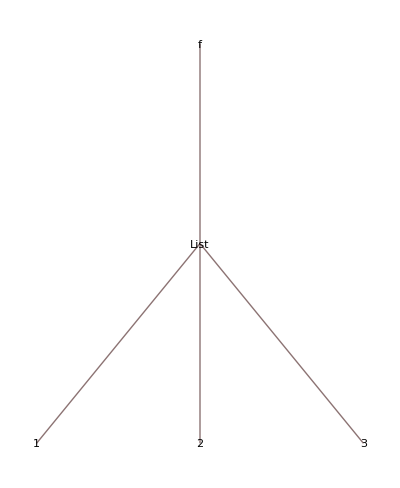

```mathematica
expr2//TreeForm
```

```mathematica
Depth[expr2]
```

3

```mathematica
LeafCount[expr2]
```

5

范例三

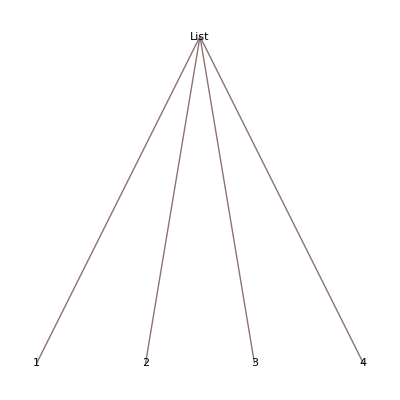

```mathematica
{1,2,3,4}//TreeForm
```

```mathematica
Depth[{1,2,3,4}]
```

2

```mathematica
LeafCount[{1,2,3,4}]
```

5

```mathematica
ClearAll["Global`*"]
```

# 赋值

## 设置值

#### Set

赋值的最简单格式是使用 Set (=) 赋值：

```mathematica
x=5
```

5

```mathematica
x
```

5

```mathematica
x+10
```

15

```mathematica
Set[x,5] (* functional form of x = 5 *)
```

```mathematica
x=RandomInteger[10]
```

8

```mathematica
{x,x,x,x}
```

{8,8,8,8}

#### SetDelayed

SetDelayed 用于延迟计算：

```mathematica
Clear[x]
x:=RandomInteger[10]
```

```mathematica
x
```

9

```mathematica
x
```

3

```mathematica
x
```

9

```mathematica
x
```

3

```mathematica
x
```

3

```mathematica
x
```

4

```mathematica
{x,x,x,x}
```

{6,0,9,6}

使用 Information (?) 查找符号的定义：

```mathematica
?x
```

#### 保护符号

系统定义的符号不能被赋值，因为它们是被保护的：

```mathematica
?List
```

```mathematica
List=2
```

Set::wrsym: 符号 List 被保护.

2

```mathematica
ClearAll["Global`*"]
```

## 清除值

#### Unset

```mathematica
x=3
```

3

```mathematica
x=.
```

```mathematica
x
```

x

#### Clear

```mathematica
Clear[x]
```

```mathematica
?x
```

Unset 和 Clear 之间的差别：

```mathematica
fact[1]=1;
fact[n_]:=n fact[n-1]
```

```mathematica
fact[1]=. (* removes a particular definition of fact *)
```

```mathematica
Definition[fact]
```

fact[n_]:=n fact[n-1]

```mathematica
Clear[fact] (* removes all definctions of fact *)
```

```mathematica
Definition[fact]
```

Null

#### Remove

```mathematica
Remove[x]
```

```mathematica
?x
```

Missing[UnknownSymbol,x]

```mathematica
Remove[f]
```

```mathematica
SyntaxInformation[f]={"ArgumentsPattern"->{_,_}};
```

```mathematica
{f[x],f[x,y],f[x,y,z]};
```

```mathematica
ClearAll[f]
```

```mathematica
{f[x],f[x,y],f[x,y,z]};
```

```mathematica
Remove[f]
```

```mathematica
{f[x],f[x,y],f[x,y,z]};
```

```mathematica
ClearAll["Global`*"]
```

# 一些基本函数

## 迭代

#### 传统循环

For 循环：

```mathematica
For[i=1,i≤10,i++,Print[i]]
```

1

2

3

4

5

6

7

8

9

10

While 循环：

```mathematica
i=1;
While[i≤10,Print[i];i++]
```

1

2

3

4

5

6

7

8

9

10

Do 循环：

```mathematica
Do[Print[i],{i,1,10}]
```

1

2

3

4

5

6

7

8

9

10

#### Table 和 Map

生成一个表达式的 n 个副本的列表：

```mathematica
Table[x^2,{x,1,10}]
```

{1,4,9,16,25,36,49,64,81,100}

把函数映射到列表或表达式的每个元素：

```mathematica
Map[f,{1,2,3,4,5}]
```

{f[1],f[2],f[3],f[4],f[5]}

```mathematica
f/@{1,2,3,4,5} (* 简写形式 *)
```

{f[1],f[2],f[3],f[4],f[5]}

```mathematica
Map[f, anyhead[1,2, 3,4,5]] (* 适用于任何标头，不一定是列表 *)
```

anyhead[f[1],f[2],f[3],f[4],f[5]]

MapThread 可以将任何函数映射到多个参数列表：

```mathematica
MapThread[f,{{a,b,c},{x,y,z}}]
```

{f[a,x],f[b,y],f[c,z]}

#### Nest 和 Fold

Nest 可以将一个函数重复应用到一个表达式：

```mathematica
Nest[f,x,5]
```

f[f[f[f[f[x]]]]]

```mathematica
NestList[f,x,5]
```

{x,f[x],f[f[x]],f[f[f[x]]],f[f[f[f[x]]]],f[f[f[f[f[x]]]]]}

Fold 可以递归处理列表的组成部分并构建一个返回值：

```mathematica
Fold[f,x,{a1,a2,a3,a4}]
```

f[f[f[f[x,a1],a2],a3],a4]

```mathematica
FoldList[f,x,{a1,a2,a3,a4}]
```

{x,f[x,a1],f[f[x,a1],a2],f[f[f[x,a1],a2],a3],f[f[f[f[x,a1],a2],a3],a4]}

```mathematica
ClearAll["Global`*"]
```

## 计数和分组

#### 计数

计算元素在列表中出现的次数：

```mathematica
Counts[{a,c,d,b,a,c,b}]
```

<|a→2,c→2,d→1,b→2|>

计算把函数 EvenQ 应用于列表元素后每个不同值出现的次数：

```mathematica
CountsBy[{1,2,3,2,1,1},EvenQ]
```

<|False→4,True→2|>

#### 分组

收集为子列表：

```mathematica
Gather[{1,2,3,1,1,2,3,4}]
```

{{1,1,1},{2,2},{3,3},{4}}

有条件收集——当应用条件时出现同样值：

```mathematica
GatherBy[{1,2,3,4,5},OddQ]
```

{{1,3,5},{2,4}}

```mathematica
GatherBy[{{a,b},{a,c},{b,c},{b,e},{x,y},{x,10}},First]
```

{{{a,b},{a,c}},{{b,c},{b,e}},{{x,y},{x,10}}}

GroupBy 与 GatherBy 一样，除了它返回的是关联：

```mathematica
GroupBy[{{a,b},{a,c},{b,c}},First]
```

<|a→{{a,b},{a,c}},b→{{b,c}}|>

```mathematica
ClearAll["Global`*"]
```

# 列表与关联

## 列表

List 是对象收集. 它包含封闭在花括号中的 Wolfram 语言表达式的序列.

### 范例

```mathematica
{a,b,c,d,e} (* 变量列表 *)
```

```mathematica
{1,3.4,-5,7.8} (* 数字列表 *)
```

```mathematica
{"Alice","Bob","Charlie"} (* 字符串列表 *)
```

```mathematica
{{1,2},{3,4}}  (* 嵌套列表表示整数矩阵 *)
```

```mathematica
MatrixForm[{{1,2},{3,4}} ]
```

(1 | 2
3 | 4)

还可以使用列表：

指定图形的区间：

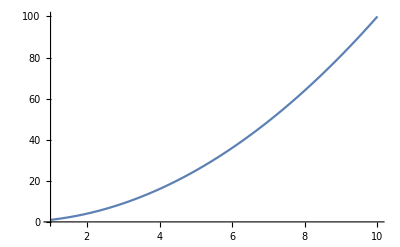

```mathematica
Plot[x^2,{x,1,10}]
```

在重复计算中创建迭代：

```mathematica
Do[Print[n^2],{n,4,8}]
```

16

25

36

49

64

```mathematica
ClearAll["Global`*"]
```

## 列表（续）

#### 构建列表

有许多可以快速创建列表的内置函数：

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Table[i,{i,1,10}]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
RandomReal[1.0,{2,3}]
```

{{0.621632,0.363769,0.392172},{0.955497,0.345431,0.635277}}

#### 列表长度

列表有多长？Length 可以提供列表中的元素数目：

```mathematica
Length[{a,42,3.14,RGBColor[1, 0, 0],"hello", x^2+3 y^3,-Graphics3D-}]
```

7

对于嵌套列表，例如多维数组（每个级别具有相同数量的元素），Dimensions 函数可用于确定每个级别的长度：

```mathematica
Dimensions[{{f[1,1],f[1,2]},{f[2,1],f[2,2]},{f[3,1],f[3,2]}}]
```

{3,2}

```mathematica
ClearAll["Global`*"]
```

## 列表（续）

#### 提取列表中的元素

```mathematica
myList = {a,b,c,d,e};
```

获取列表中 First 或 Last 元素：

```mathematica
{First[myList],Last[myList]}
```

{a,e}

Part 函数是从列表中提取元素更通用的方法：

```mathematica
Part[{a,b,c,d,e},2]
```

b

```mathematica
myList[[2]] (* 简写形式 *)
```

b

```mathematica
myList[[-1]]
myList[[3;;5]]
myList[[{1,4}]]
```

e

{c,d,e}

{a,d}

#### 修改列表

```mathematica
myList = {a,b,c,d,e};
```

通过使用 Part 函数修改列表：

```mathematica
myList[[2]]=b1;
myList (* 可变性 *)
```

{a,b1,c,d,e}

```mathematica
myList[[4]]=d1;
myList (* 可变性 *)
```

{a,b1,c,d1,e}

```mathematica
AppendTo[myList,x1]; (* 就地修改 *)
myList
```

{a,b1,c,d1,e,x1}

```mathematica
PrependTo[myList,y1]; (* 就地修改 *)
myList
```

{y1,a,b1,c,d1,e,x1}

```mathematica
Append[myList,x2](* 创建新的副本 *)
myList
```

{y1,a,b1,c,d1,e,x1,x2}

{y1,a,b1,c,d1,e,x1}

```mathematica
Prepend[myList,x2] (* 创建新的副本 *)
myList
```

{x2,y1,a,b1,c,d1,e,x1}

{y1,a,b1,c,d1,e,x1}

```mathematica
ClearAll["Global`*"]
```

## 关联

关联是含有键值对的字典数据结构.

关联提供广义的符号索引列表、关联数组、字典、哈希图等. 关联将标记的数据表示为 key → value pairs：

```mathematica
Association[{a->1,b->2}]
```

<|a→1,b→2|>

返回列表：

```mathematica
Normal[<|a->1,b->2|>]
```

{a→1,b→2}

关联可以使用任何 Wolfram 语言表达式作为键或值：

```mathematica
assoc=<|a->1,{2,3}->100,4->200,"cat"->-Graphics-|>
```

<|a→1,{2,3}→100,4→200,cat→-Graphics-|>

关联可以细分为只有 Keys 或 Values 的列表：

```mathematica
Keys[assoc]
```

{a,{2,3},4,cat}

```mathematica
Values[assoc]
```

{1,100,200,-Graphics-}

键必须是唯一的. 如果不唯一，只保留最后一对 key → value：

```mathematica
<|a->1,b->2,c->3,d->4,b->10|>
```

<|a→1,b→10,c→3,d→4|>

```mathematica
ClearAll["Global`*"]
```

## 访问元素

```mathematica
assoc=<|a->1,{2,3}->100,4->200,"cat"->-Graphics-|>;
```

关联可以细分为只有 Keys 或 Values 的列表：

```mathematica
Keys[assoc]
```

{a,{2,3},4,cat}

```mathematica
Values[assoc]
```

{1,100,200,-Graphics-}

对应于特殊键的值：

```mathematica
assoc[a] (* 注意与 Part 函数不同的是这里只有单个方括号 *)
```

1

```mathematica
assoc["cat"]
```

-Graphics-

也使用 Part 函数：

```mathematica
assoc[[1]]
```

1

```mathematica
assoc[[4]]
```

-Graphics-

### Lookup

从关联对象提取值的另一种更通用的方法是使用函数 Lookup：

```mathematica
assoc=<|a->1,{2,3}->100,4->200,"cat"->-Graphics-|>;
```

```mathematica
Lookup[assoc,a]
```

1

```mathematica
Lookup[assoc,{a,"cat"}]
```

{1,-Graphics-}

Lookup 可以遍历关联列表：

```mathematica
table={
<|a->1,b->2|>,
<|a->3,b->1|>,
<|a->4,b->3|>
};
```

```mathematica
Lookup[table,a]
```

{1,3,4}

```mathematica
Lookup[table,b]
```

{2,1,3}

```mathematica
ClearAll["Global`*"]
```

## 构建和修改关联

#### 规则列表

```mathematica
ruleList={a->1,b->2,c->3,d->4};
<|ruleList|>
Association[ruleList]
```

<|a→1,b→2,c→3,d→4|>

<|a→1,b→2,c→3,d→4|>

#### 键和值列表

```mathematica
myKeys={a,b,c,d};
myValues={1,2,3,4};
```

```mathematica
AssociationThread[myKeys,myValues]
```

<|a→1,b→2,c→3,d→4|>

#### 键和函数列表

```mathematica
AssociationMap[f,{a,b,c,d}]
```

<|a→f[a],b→f[b],c→f[c],d→f[d]|>

```mathematica
myKeys={1,2,3,4};
```

```mathematica
AssociationMap[#^2&,myKeys]
```

<|1→1,2→4,3→9,4→16|>

#### 添加新的键-值对

```mathematica
myKeys={a,b,c,d};
myValues={1,2,3,4};
assoc=AssociationThread[myKeys,myValues]
```

<|a→1,b→2,c→3,d→4|>

```mathematica
newAssoc=AssociateTo[assoc,e->5]
```

<|a→1,b→2,c→3,d→4,e→5|>

#### 去除键-值对

```mathematica
newAssoc
```

<|a→1,b→2,c→3,d→4,e→5|>

```mathematica
KeyDropFrom[newAssoc,d]
```

<|a→1,b→2,c→3,e→5|>

```mathematica
ClearAll["Global`*"]
```

## 创建关联的函数

#### Counts

Counts 返回一个包含不同元素作为键，计数作为值的关联对象. 类似于 Tally，它返回列表对象：

```mathematica
RandomInteger[{1,10}, 1000]
```

{1,3,10,6,3,6,2,3,7,3,1,8,6,5,4,4,5,10,9,4,4,8,9,9,5,1,6,9,7,3,1,7,2,9,4,9,6,5,8,2,10,6,4,4,1,8,8,4,4,6,6,9,10,9,6,7,8,3,7,5,5,8,7,2,2,2,7,4,5,9,10,6,7,1,10,5,6,2,7,8,9,5,7,3,5,7,7,8,7,8,3,9,5,8,3,5,4,4,1,10,3,4,8,8,9,8,7,5,8,9,5,1,8,8,10,8,10,8,4,7,2,4,2,1,5,6,9,3,4,1,5,2,9,10,10,9,4,3,7,1,2,5,10,1,4,9,2,8,3,7,1,4,8,10,2,8,1,8,2,7,9,8,9,3,2,2,6,3,5,10,10,3,5,3,1,9,8,6,8,5,6,10,5,10,3,3,5,6,6,7,9,2,1,8,3,3,8,2,9,10,8,8,8,1,9,5,5,7,3,3,4,6,5,4,5,4,8,2,10,7,1,1,2,2,1,2,10,6,10,5,3,2,2,3,6,9,2,3,3,10,10,6,7,9,1,6,6,10,3,9,6,1,7,2,4,3,10,7,4,3,1,2,10,10,10,2,10,2,6,2,7,10,2,3,6,2,9,1,9,7,4,7,9,3,1,9,5,7,2,6,8,6,8,5,6,8,3,6,6,3,10,7,8,1,6,9,9,10,6,7,6,8,9,3,8,2,3,4,3,2,4,2,2,5,6,10,7,8,7,4,10,9,7,1,8,2,9,9,7,4,10,9,6,5,5,4,7,7,3,4,4,10,10,6,2,3,3,6,10,2,2,8,10,6,9,6,4,2,2,5,6,3,6,9,3,2,3,5,1,5,8,3,10,1,8,4,2,7,2,5,2,1,3,9,10,3,8,3,5,10,8,10,2,4,6,10,10,8,9,9,2,10,1,10,7,6,7,8,3,8,1,1,3,1,6,8,5,7,5,10,6,8,8,5,1,2,5,9,6,9,3,8,9,7,5,4,1,2,10,2,5,3,9,2,5,7,7,10,6,8,10,7,6,1,7,4,9,10,10,7,10,7,8,4,5,6,1,9,6,2,9,6,10,2,5,3,7,10,8,10,1,6,3,3,10,6,5,8,3,2,8,2,3,2,7,10,7,4,4,1,8,1,3,1,9,8,2,3,1,10,8,3,9,9,8,2,3,2,5,6,6,7,4,2,3,1,7,6,7,6,8,1,7,1,2,9,7,3,8,7,1,4,8,3,8,10,1,8,10,3,6,9,5,3,3,1,3,8,2,4,7,8,9,7,4,3,10,1,1,2,10,4,5,3,1,4,3,3,8,1,7,4,1,7,4,4,6,8,6,4,7,4,7,2,3,4,10,6,4,8,7,6,9,1,1,3,8,8,1,2,9,4,5,10,6,2,4,3,5,2,2,9,6,5,8,9,2,7,2,2,3,7,7,10,10,1,3,9,6,7,2,5,2,3,5,9,6,6,7,1,7,6,8,5,1,4,2,6,5,3,1,8,3,1,9,4,4,1,6,2,10,6,7,8,2,3,1,10,2,10,1,3,9,3,9,1,7,10,2,8,2,9,2,3,3,8,1,4,2,4,1,7,3,1,8,2,9,5,9,5,1,5,5,4,8,5,6,2,7,7,6,2,6,5,8,6,10,7,2,6,8,9,8,2,10,4,5,7,6,1,5,5,4,3,7,9,8,7,10,5,10,2,4,1,10,3,2,6,2,1,2,1,5,1,9,9,6,7,6,9,6,4,4,3,1,10,7,5,3,10,5,9,8,5,9,7,3,6,2,10,10,2,4,10,2,8,3,9,10,8,1,6,1,4,8,6,6,8,7,5,4,4,4,8,9,7,6,9,4,6,6,8,8,3,4,7,8,7,1,5,2,8,10,6,1,3,9,10,10,9,10,9,1,9,3,1,5,8,9,1,2,7,4,7,9,6,4,3,5,2,3,3,5,1,2,8,4,10,3,1,2,4,10,8,8,6,2,8,4,8,7,2,9,9,10,9,4,3,2,10,8,9,2,10,5,2,7,7,10,8,2,9,6,3,6,7,3,2,7,9,1,10,1,1,2,10,2,6,6,10,9,1,2,10,10,5,1,6,7,8,10,1,9,3,8,2,3,1,1,10,8,4,4,3,5,10,10,6,3,3,7,1,9,7,4,1,5,7,7,9,2,7,7,8,4,1,10,10,3,6,3,9,8,9,3,8,5,2,8,2,1,1,9,9,9,6,10,2,7,9}

```mathematica
SeedRandom[1]
Counts[RandomInteger[{1,10}, 1000]]
```

<|2→104,5→96,1→92,8→103,9→112,7→90,6→105,4→104,3→97,10→97|>

#### PositionIndex

类似于 Counts，PositionIndex 返回一个包含不同元素作为键，位置作为值的关联对象：

```mathematica
Characters["This is a string"]
```

{T,h,i,s, ,i,s, ,a, ,s,t,r,i,n,g}

```mathematica
PositionIndex[Characters["This is a string"]]
```

<|T→{1},h→{2},i→{3,6,14},s→{4,7,11}, →{5,8,10},a→{9},t→{12},r→{13},n→{15},g→{16}|>

#### WordCounts

WordCounts 产生字符串中单词的计数，并以关联形式返回信息. 两参数版本返回 n-元：

```mathematica
WordCounts[
"It matters not how strait the gate,
How charged with punishments the scroll.
I am the master of my fate:
I am the captain of my soul. "]
```

<|the→4,my→2,of→2,am→2,I→2,soul→1,captain→1,fate→1,master→1,scroll→1,punishments→1,with→1,charged→1,How→1,gate→1,strait→1,how→1,not→1,matters→1,It→1|>

#### GroupBy

GroupBy 产生一种关联，其中根据分组功能对元素进行分组. 它类似于 GatherBy，后者返回列表，但功能更强大.

这是一个示例，其中具有共同的第一个元素的子列表被合在一起，仅保留第二个元素：

```mathematica
GroupBy[{{a,10},{b,20},{a,30}},First->Last]
```

<|a→{10,30},b→{20}|>

#### EntityValue

EntityValue 也可以使用第三个参数返回关联对象.

"EntityAssociation":

```mathematica
EntityValue[
	EntityClass["Country","NATO"],
	"Population",
	"EntityAssociation"
]
```

<|Albania→2880913 people,Belgium→11539326 people,Bulgaria→7000117 people,Canada→37411038 people,Croatia→4130299 people,Czech Republic→10689213 people,Denmark→5771877 people,Estonia→1325649 people,France→65129731 people,Germany→83517046 people,Greece→10473452 people,Hungary→9684680 people,Iceland→339037 people,Italy→60550092 people,Latvia→1906740 people,Lithuania→2759631 people,Luxembourg→615730 people,North Macedonia→2083458 people,Montenegro→627988 people,Netherlands→17097123 people,Norway→5378859 people,Poland→37887771 people,Portugal→10226178 people,Romania→19364558 people,Slovakia→5457012 people,Slovenia→2078654 people,Spain→46736782 people,Turkey→83429607 people,United Kingdom→67530161 people,United States→329064917 people|>

```mathematica
ClearAll["Global`*"]
```

## Dataset

数据集的一个简单示例是由关联的关联组成：

```mathematica
data=Dataset[<|"a"-><|"x"->1,"y"->2,"z"->3|>,"b"-><|"x"->5,"y"->10,"z"->7|>|>]
```

访问数据集的各个部分基本上与列表和关联中的相同：

```mathematica
data["b"]
```

Wolfram 语言还具有数据集形式的内置数据：

```mathematica
planets=ExampleData[{"Dataset","Planets"}]
```

```mathematica
planets["Mercury"]["Radius"]
```

2439.7 km

```mathematica
Select[planets, #["Radius"]>Quantity[50000,"Kilometers"]&]
```

```mathematica
ClearAll["Global`*"]
```

## 总结

Wolfram 语言具有许多原子，其中一些是：Integer、Real、String、Rational 和 Symbol. 原子可以组合形成复合表达式.

Wolfram 语言中的一切都是表达式. 表达式具有常用的格式 f[e1, e2, e3,...]，其中 e1、e2 等可以是原子对象或表达式自身.

用于检查表达式解剖结构的函数包括 Head、Length、Part、 Level、 Depth 和 LeafCount.

Set 用于直接赋值. SetDelayed 用于延迟赋值.

Table、Map、Nest 和 Fold 提供非传统的迭代方式.

Wolfram 语言中的列表可以包含任何表达式类型.

Association 以 键→值对的形式表示数据.

操作列表和关联有各种函数.